### The asymptotic properties of y_R(k)

```mathematica
(1+y^(2 k-1)) (1+y^(1+2 k))==2//TeXForm
```

\left(y^{2 k-1}+1\right) \left(y^{2 k+1}+1\right)=2

```mathematica
Manipulate[Plot[{(1+y^(2 k-1))^2,(1+y^(2 k-1)) (1+y^(1+2 k)),(1+y^(2 k+1))^2,2},{y,0,1},PlotRange->{0,4}],{k,1,8,1}]
```

```mathematica
Solve[(1+y^(2 k-1)) (1+y^(2 k-1))==2,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{y->(-1-√2)^(1/(-1+2 k))},{y->(-1+√2)^(1/(-1+2 k))}}//N
```

{{y→(-2.41421)^(1/(-1.+2. k))},{y→0.414214^(1/(-1.+2. k))}}

```mathematica
Solve[(1+y^(2 k+1)) (1+y^(2 k+1))==2,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→(-1-√2)^(1/(1+2 k))},{y→(-1+√2)^(1/(1+2 k))}}

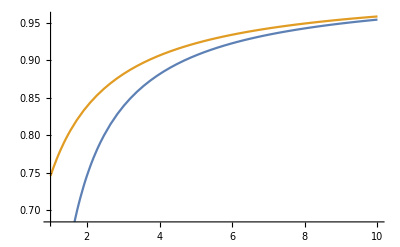

```mathematica
Plot[{(-1+√2)^(1/(-1+2 k)),(-1+√2)^(1/(1+2 k))},{k,1,10}]
```

```mathematica
(-1+√2)^(1/(1+2 k))//TeXForm
```

\left(\sqrt{2}-1\right)^{\frac{1}{2 k+1}}

```mathematica
Series[(-1+√2)^(1/(1+2 k)),{k,∞,3}]//Normal
```

1+Log[-1+√2]/(2 k)+(-2 Log[-1+√2]+Log[-1+√2]^2)/(8 k^2)+(6 Log[-1+√2]-6 Log[-1+√2]^2+Log[-1+√2]^3)/(48 k^3)

```mathematica
Series[(-1+√2)^(1/(-1+2 k)),{k,∞,3}]//Normal
```

1+Log[-1+√2]/(2 k)+(2 Log[-1+√2]+Log[-1+√2]^2)/(8 k^2)+(6 Log[-1+√2]+6 Log[-1+√2]^2+Log[-1+√2]^3)/(48 k^3)

```mathematica
1+Log[-1+√2]/(2 k)//TeXForm
```

\frac{\log \left(\sqrt{2}-1\right)}{2 k}+1

```mathematica
Log[-1+√2]/(2 k)//N
```

-0.440687/k

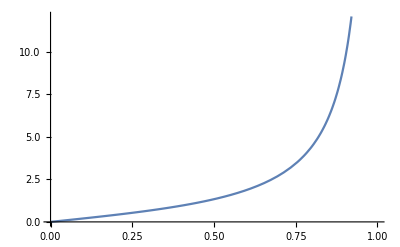

```mathematica
Plot[2 y/(1-y^2),{y,0,1}]
```

Back to the ν variable

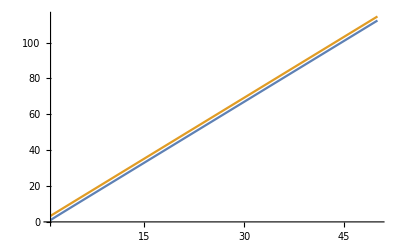

```mathematica
Plot[{2 y/(1-y^2)/.y->(-1+√2)^(1/(-1+2 k)),2 y/(1-y^2)/.y->(-1+√2)^(1/(1+2 k))},{k,1,50}]
```

```mathematica
{2 y/(1-y^2)/.y->(-1+√2)^(1/(-1+2 k)),2 y/(1-y^2)/.y->(-1+√2)^(1/(1+2 k))}//Simplify
```

```mathematica
Simplify[{(2 (-1+√2)^(1/(1-2 k)))/(-1+(-1+√2)^(2/(1-2 k))),-(2 (-1+√2)^(1/(1+2 k)))/(-1+(-1+√2)^(2/(1+2 k)))},k∈Integers&&k>0]//FunctionExpand
```

```mathematica
{(2 (-1+√2)^(1/(1-2 k)))/(-1+(-1+√2)^(2/(1-2 k))),-(2 (-1+√2)^(1/(1+2 k)))/(-1+(-1+√2)^(2/(1+2 k)))}/.k->1.
```

{1.,3.3553}

```mathematica
FullSimplify[(2 (√2+1)^(1/(2 k-1)))/((√2+1)^(2/(2 k-1))-1)==(2 (-1+√2)^(1/(1-2 k)))/(-1+(-1+√2)^(2/(1-2 k)))]
```

```mathematica
FullSimplify[(2 (√2-1)^(1/(2 k+1)))/(1-(√2-1)^(2/(1+2 k)))==-(2 (-1+√2)^(1/(1+2 k)))/(-1+(-1+√2)^(2/(1+2 k)))]
```

True

```mathematica
Series[(2 (√2+1)^(1/(2 k-1)))/((√2+1)^(2/(2 k-1))-1),{k,∞,2}]
```

```mathematica
(2 k)/Log[1+√2]-1/Log[1+√2]-Log[1+√2]/(12 k)-Log[1+√2]/(24 k^2)+O[1/k]^3//N
```

2.26919 k-1.13459-0.0734478/k-0.0367239/k^2+O[1/k]^3

```mathematica
2.269185314213022
```

```mathematica
1.134592657106511
```

```mathematica
(2 k)/Log[1+√2]-1/Log[1+√2]//TeXForm
```

\frac{2 k}{\log \left(1+\sqrt{2}\right)}-\frac{1}{\log \left(1+\sqrt{2}\right)}

```mathematica
Series[(2 (√2-1)^(1/(2 k+1)))/(1-(√2-1)^(2/(1+2 k))),{k,∞,2}]
```

```mathematica
-(2 k)/Log[-1+√2]-1/Log[-1+√2]+Log[-1+√2]/(12 k)-Log[-1+√2]/(24 k^2)+O[1/k]^3//N
```

2.26919 k+1.13459-0.0734478/k+0.0367239/k^2+O[1/k]^3

```mathematica
(2 (√2+1)^(1/(2 k-1)))/((√2+1)^(2/(2 k-1))-1)//TeXForm
```

\frac{2 \left(1+\sqrt{2}\right)^{\frac{1}{2 k-1}}}{\left(1+\sqrt{2}\right)^{\frac{2}{2
   k-1}}-1}

```mathematica
(2 (√2-1)^(1/(2 k+1)))/(1-(√2-1)^(2/(1+2 k)))//TeXForm
```

\frac{2 \left(\sqrt{2}-1\right)^{\frac{1}{2 k+1}}}{1-\left(\sqrt{2}-1\right)^{\frac{2}{2
   k+1}}}

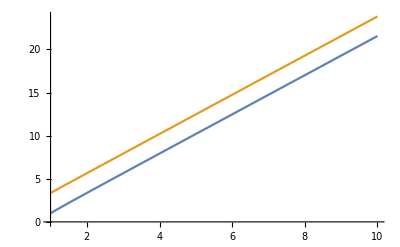

```mathematica
Plot[{(2 (√2+1)^(1/(2 k-1)))/((√2+1)^(2/(2 k-1))-1),(2 (√2-1)^(1/(2 k+1)))/(1-(√2-1)^(2/(1+2 k)))},{k,1,10}]
```

```mathematica
1/(√2-1)//FullSimplify
```

```mathematica
(1+√2)^2//Expand
```

3+2 √2

```mathematica
(-1+√2)^(2/(1-2 k))/.k->1.
```

5.82843

```mathematica
(√2+1)^(2/(2 k-1))/.k->1.
```

5.82843

```mathematica
FullSimplify[(2 (√2+1)^(1/(2 k-1)))/((√2+1)^(2/(2 k-1))-1)==(2 (-1+√2)^(1/(1-2 k)))/(-1+(-1+√2)^(2/(1-2 k)))]
```

True

```mathematica
(2 (√2+1)^(1/(2 k-1)))/((√2+1)^(2/(2 k-1))-1)/.k->1.
```

1.

```mathematica
(-1+√2)^(2/(1-2 k))-1/.k->3.
```

0.42269

```mathematica
-1+(-1+√2)^(2/(1+2 k))/.k->3.
```

-0.222616

```mathematica
Series[(2 (-1+√2)^(1/(1-2 k)))/(-1+(-1+√2)^(2/(1-2 k))),{k,∞,3}]
```

```mathematica
-(2 k)/Log[-1+√2]+1/Log[-1+√2]+Log[-1+√2]/(12 k)+Log[-1+√2]/(24 k^2)+(60 Log[-1+√2]-7 Log[-1+√2]^3)/(2880 k^3)+O[1/k]^4//N
```

```mathematica
2.2691853142130225 k-1.1345926571065112-0.07344779891829523/k-0.03672389945914761/k^2-0.01669782587309219/k^3+O[1/k]^4//Normal
```

-1.13459-0.0166978/k^3-0.0367239/k^2-0.0734478/k+2.26919 k

```mathematica
Series[-(2 (-1+√2)^(1/(1+2 k)))/(-1+(-1+√2)^(2/(1+2 k))),{k,∞,3}]
```

```mathematica
-(2 k)/Log[-1+√2]-1/Log[-1+√2]+Log[-1+√2]/(12 k)-Log[-1+√2]/(24 k^2)+(60 Log[-1+√2]-7 Log[-1+√2]^3)/(2880 k^3)+O[1/k]^4//N
```

```mathematica
2.2691853142130225 k+1.1345926571065112-0.07344779891829523/k+0.03672389945914761/k^2-0.01669782587309219/k^3+O[1/k]^4//Normal
```

1.13459-0.0166978/k^3+0.0367239/k^2-0.0734478/k+2.26919 k

```mathematica
With[{k=10,θ=1-1/21},1/θ{-1.1345926571065112+2.2691853142130225 k,1.1345926571065112+2.2691853142130225 k,-0.07344779891829523/k+2.2691853142130225 k}]
```

{22.6351,25.0178,23.8187}

```mathematica
With[{m=21,θ=1-1/21},A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Reduce[ν>0&&And@@Thread[0≤{First[#],Last[#]}&@((Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]])]]]
```

ν≥Root[-13248496640331026125580781-54075496491147045410533800 #1^2-92646353272814287929360000 #1^4-86504531533906898160000000 #1^6-47812878824013166500000000 #1^8-15901486532551620000000000 #1^10-3090667936356000000000000 #1^12-323460799200000000000000 #1^14-15280650000000000000000 #1^16-210000000000000000000 #1^18+10000000000000000000 #1^19&,1]

```mathematica
ν≥Root[-13248496640331026125580781-54075496491147045410533800 #1^2-92646353272814287929360000 #1^4-86504531533906898160000000 #1^6-47812878824013166500000000 #1^8-15901486532551620000000000 #1^10-3090667936356000000000000 #1^12-323460799200000000000000 #1^14-15280650000000000000000 #1^16-210000000000000000000 #1^18+10000000000000000000 #1^19&,1]//N
```

ν≥23.8002

```mathematica
With[{m=21,θ=1/21},A =DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;Reduce[ν>0&&And@@Thread[0≤{Last[#]}&@((Inverse[IdentityMatrix[Length[A]]-θ ν A].(IdentityMatrix[Length[A]]+(1-θ) ν A))[[1]])]]]
```

```mathematica
ν≥Root[-6946027806565873025328496508928-70877834760876255360494862336 #1^2-303583570404357858686926848 #1^4-708645122325765309726720 #1^6-979207758315789649920 #1^8-814156110466642944 #1^10-395605495853568 #1^12-103507455744 #1^14-12224520 #1^16-420 #1^18+#1^19&,1]//N
```

ν≥476.003

```mathematica
With[{k=10,θ=1/21},1/θ{-1.1345926571065112+2.2691853142130225 k,1.1345926571065112+2.2691853142130225 k,-0.07344779891829523/k+2.2691853142130225 k}]
```

{452.702,500.355,476.375}